```mathematica
δ=Association[{0, "1"}-> 0, {0, "0"}-> 1,{1, "0"}-> 1,{1, "1"}-> 2,{2, "0"}-> 2,{2, "1"}-> 2]
```

<|{0,1}→0,{0,0}→1,{1,0}→1,{1,1}→2,{2,0}→2,{2,1}→2|>

```mathematica
δ[{0, "1"}]
```

0

```mathematica
Fold[δ[{#1, #2}]&, 0,{"1","0","1","0"}]
```

2

```mathematica
FoldList[δ[{#1, #2}]&, 0,{"1","0","1","0"}]
```

{0,0,1,2,2}

## Funcion extendida de δ

```mathematica
DeltaHat[δ_, q0_, string_] := FoldList[δ[{#1, #2}]&, q0,Characters[string]]
```

```mathematica
DeltaHat[δ, 0, "01011"]
```

{0,1,2,2,2,2}

## Aceptar un string

```mathematica
IsValid[δ_, q0_,qf_, string_] := Fold[δ[{#1, #2}]&, q0,Characters[string]] == qf;
```

```mathematica
IsValid[δ, 0, 2,"01011"]
```

True

```mathematica
IsValid[δ, 0, 2,"11111"]
```

False

```mathematica
Tuples[{0,1} ,2]
```

{{0,0},{0,1},{1,0},{1,1}}

```mathematica
StringJoin /@ Tuples[{"0","1"} ,2]
```

{00,01,10,11}

## Ejemplo libro 2.4 / Tanto el numero de ceros como de unos es par

```mathematica
δ=Association[{0, "1"}-> 1, {0, "0"}-> 2,{1, "0"}-> 3,{1, "1"}-> 0,{2, "0"}-> 0,{2, "1"}-> 3,{3, "0"}-> 1,{3, "1"}-> 2]
```

<|{0,1}→1,{0,0}→2,{1,0}→3,{1,1}→0,{2,0}→0,{2,1}→3,{3,0}→1,{3,1}→2|>

```mathematica
DeltaHat[δ_, q0_, string_] := FoldList[δ[{#1, #2}]&, q0,Characters[string]]
```

```mathematica
DeltaHat[δ, 0, "010101010101"]
```

{0,2,3,1,0,2,3,1,0,2,3,1,0}

```mathematica
IsValid[δ_, q0_,qf_, string_] := Fold[δ[{#1, #2}]&, q0,Characters[string]] == qf;
```

```mathematica
IsValid[δ, 0, 0,"01011"]
```

False

```mathematica
IsValid[δ, 0, 0,"010101010101"]
```

True

```mathematica
Tally[Map[IsValid[δ,0,0,#]&,Map[StringJoin,Tuples[{"0","1"},6]]]]
```

{{True,32},{False,32}}

## Ejercicio Extra Autómata que acepta strings que comienzan y terminan en “a”, o comienzan y terminan en “b”

```mathematica
DeltaHat[δ_,q0_,string_]:=FoldList[δ[{#1,#2}]&,q0,Characters[string]]
```

```mathematica
δ=Association[{0, "a"}-> 1, {0, "b"}-> 2,{1, "a"}-> 1,{1, "b"}-> 3,{3, "a"}-> 1,{3, "b"}-> 3, {2, "b"}-> 2, {2, "a"}-> 4,{4, "a"}-> 4,{4, "b"}-> 2]
```

<|{0,a}→1,{0,b}→2,{1,a}→1,{1,b}→3,{3,a}→1,{3,b}→3,{2,b}→2,{2,a}→4,{4,a}→4,{4,b}→2|>

```mathematica
DeltaHat[δ, 0, "aabaa"]
```

{0,1,1,3,1,1}

```mathematica
DeltaHat[δ, 0, "bbbbaab"]
```

{0,2,2,2,2,4,4,2}

```mathematica
IsValid[δ_, q0_,qf_, string_] := Fold[δ[{#1, #2}]&, q0,Characters[string]] == qf;
```

```mathematica
IsValid[δ, 0,1,"aabaa"]
```

True

```mathematica
IsValid[δ, 0,2,"bbbbaab"]
```

True

## Build a Graph Representation

```mathematica
ToEdges[δ_]:=MapThread[DirectedEdge,{First/@Keys[δ],Values[δ]}];
ToVertexLabels[s_]:=Table[Rule[i-1,Placed[i-1,Center]],{i,1,s}];
ToEdgeLabels[δ_]:=MapThread[Rule,{ToEdges[δ],Last/@Keys[δ]}];
```

```mathematica
UnifyLabels[labels_]:=If[Length[#]>1,First[Keys[#]]->(Values[#]&/@#),First[#]]&/@GatherBy[labels,First];
```

```mathematica
UnifyEdges[edges_]:=First/@Gather[edges];
```

```mathematica
ShowGraph[δ_,s_,q0_,q_List]:=Graph[UnifyEdges[ToEdges[δ]],VertexSize->Large,VertexLabels->ToVertexLabels[s],EdgeLabels->UnifyLabels[ToEdgeLabels[δ]],VertexStyle->Join[{0->White},Map[(#->Red)&,q]]]
```

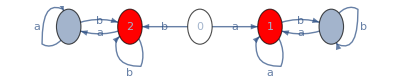

```mathematica
ShowGraph[δ,5,0,{1,2}]
```